```mathematica
$LoadFeynArts=True;
<<FeynCalc`
$FAVerbose=False;
```

FeynCalc 9.1.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

FeynArts 3.9 patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

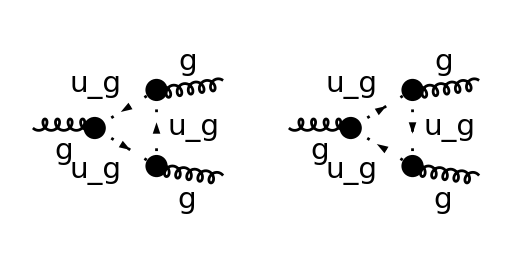

```mathematica
top=CreateTopologies[1,1->2,ExcludeTopologies->{WFCorrections,SelfEnergies,Tadpoles}];
diags=InsertFields[top,{V[5]}->{V[5],V[5]},Model->"SMQCD",InsertionLevel -> {Particles},ExcludeParticles->{F[__],S[_],V[_],U[1|2|3|4]}];
Paint[diags, ColumnsXRows -> {2, 1},SheetHeader -> False,SheetHeader->None,Numbering -> None,ImageSize->{512,256}];
```

```mathematica
amps=FCFAConvert[CreateFeynAmp[diags, Truncated -> True,GaugeRules->{},PreFactor->1],IncomingMomenta->{p1},
OutgoingMomenta->{p2,p3},LoopMomenta->{q},DropSumOver->True,UndoChiralSplittings->True,ChangeDimension->D,List->True,SMP->True,LorentzIndexNames->{λ,μ,ν},
SUNIndexNames->{a,b,c}]//Contract//SUNSimplify
```

{(ⅈ C_A g_s^3 q^μ (q-p2)^ν f^abc (-p2-p3+q)^λ)/(2 q^2.(q-p2)^2.(-p2-p3+q)^2),(ⅈ C_A g_s^3 q^λ (p2-q)^μ f^abc (p2+p3-q)^ν)/(2 q^2.(q-p2)^2.(-p2-p3+q)^2)}

```mathematica
amps[[2]]/.p3->-p2/.p2->p
```

-(ⅈ C_A g_s^3 q^λ q^ν (p-q)^μ f^abc)/(2 q^2.(q-p)^2.q^2)

## Check with Pascual and Tarrach

```mathematica
amps2=(amps/.{p2->-p2,p3->-p3});
```

```mathematica
ampsPT=(TID[#,q,ToPaVe->True,UsePaVeBasis->True]&/@amps2);
```

```mathematica
uvParts={PaVe[1,{SPD[p2,p2],SPD[p2,p2]+2 SPD[p2,p3]+SPD[p3,p3],SPD[p3,p3]},{0,0,0},PaVeAutoOrder->True,PaVeAutoReduce->True]->0,PaVe[2,{SPD[p2,p2],SPD[p2,p2]+2 SPD[p2,p3]+SPD[p3,p3],SPD[p3,p3]},{0,0,0},PaVeAutoOrder->True,PaVeAutoReduce->True]->0,PaVe[0,0,{SPD[p2,p2],SPD[p2,p2]+2 SPD[p2,p3]+SPD[p3,p3],SPD[p3,p3]},{0,0,0},PaVeAutoOrder->True,PaVeAutoReduce->True]->1/(64 EpsilonUV π^4),PaVe[1,1,{SPD[p2,p2],SPD[p2,p2]+2 SPD[p2,p3]+SPD[p3,p3],SPD[p3,p3]},{0,0,0},PaVeAutoOrder->True,PaVeAutoReduce->True]->0,PaVe[1,2,{SPD[p2,p2],SPD[p2,p2]+2 SPD[p2,p3]+SPD[p3,p3],SPD[p3,p3]},{0,0,0},PaVeAutoOrder->True,PaVeAutoReduce->True]->0,PaVe[2,2,{SPD[p2,p2],SPD[p2,p2]+2 SPD[p2,p3]+SPD[p3,p3],SPD[p3,p3]},{0,0,0},PaVeAutoOrder->True,PaVeAutoReduce->True]->0,PaVe[0,0,1,{SPD[p2,p2],SPD[p2,p2]+2 SPD[p2,p3]+SPD[p3,p3],SPD[p3,p3]},{0,0,0},PaVeAutoOrder->True,PaVeAutoReduce->True]->-1/(192 EpsilonUV π^4),PaVe[0,0,2,{SPD[p2,p2],SPD[p2,p2]+2 SPD[p2,p3]+SPD[p3,p3],SPD[p3,p3]},{0,0,0},PaVeAutoOrder->True,PaVeAutoReduce->True]->-1/(192 EpsilonUV π^4),PaVe[1,1,1,{SPD[p2,p2],SPD[p2,p2]+2 SPD[p2,p3]+SPD[p3,p3],SPD[p3,p3]},{0,0,0},PaVeAutoOrder->True,PaVeAutoReduce->True]->0,PaVe[1,1,2,{SPD[p2,p2],SPD[p2,p2]+2 SPD[p2,p3]+SPD[p3,p3],SPD[p3,p3]},{0,0,0},PaVeAutoOrder->True,PaVeAutoReduce->True]->0,PaVe[1,2,2,{SPD[p2,p2],SPD[p2,p2]+2 SPD[p2,p3]+SPD[p3,p3],SPD[p3,p3]},{0,0,0},PaVeAutoOrder->True,PaVeAutoReduce->True]->0,PaVe[2,2,2,{SPD[p2,p2],SPD[p2,p2]+2 SPD[p2,p3]+SPD[p3,p3],SPD[p3,p3]},{0,0,0},PaVeAutoOrder->True,PaVeAutoReduce->True]->0};
```

```mathematica
ampsPT2=ampsPT/.FCI[uvParts]
```

{-(C_A g_s^3 f^abc (p3^λ g^μν-p2^μ g^λν))/(128 π^2 ε_UV)-(C_A g_s^3 f^abc (p2^λ g^μν+p2^μ g^λν+p2^ν g^λμ))/(384 π^2 ε_UV)+(C_A g_s^3 f^abc (p3^λ g^μν+p3^μ g^λν+p3^ν g^λμ))/(384 π^2 ε_UV),(C_A g_s^3 f^abc (p2^λ g^μν-p3^ν g^λμ))/(128 π^2 ε_UV)-(C_A g_s^3 f^abc (p2^λ g^μν+p2^μ g^λν+p2^ν g^λμ))/(384 π^2 ε_UV)+(C_A g_s^3 f^abc (p3^λ g^μν+p3^μ g^λν+p3^ν g^λμ))/(384 π^2 ε_UV)}

```mathematica
ampsPTUVpart1=Total[ampsPT2]//FCE//Collect2[#,{Epsilon,MTD}]&
```

-(C_A g_s^3 g^λμ (2 p2^ν+p3^ν) f^abc)/(384 π^2 ε_UV)+(C_A g_s^3 g^λν (p2^μ+2 p3^μ) f^abc)/(384 π^2 ε_UV)+(C_A g_s^3 g^μν (p2^λ-p3^λ) f^abc)/(384 π^2 ε_UV)

```mathematica
(* p2+p3 = -p1 *)
ampsPTUVpart2=ampsPTUVpart1/.{FVD[p2,i_]+2FVD[p3,i_]:>FVD[p3,i]-FVD[p1,i],
FVD[p3,i_]+2FVD[p2,i_]:>FVD[p2,i]-FVD[p1,i]}
```

-(C_A g_s^3 g^λμ (p2^ν-p1^ν) f^abc)/(384 π^2 ε_UV)+(C_A g_s^3 g^λν (p3^μ-p1^μ) f^abc)/(384 π^2 ε_UV)+(C_A g_s^3 g^μν (p2^λ-p3^λ) f^abc)/(384 π^2 ε_UV)

```mathematica
PTVertexFuLorentzStruct[{p_,q_,k_},{mu_,nu_,si_},{a_,b_,c_}]:=
-I SUNF[a,b,c](MTD[mu,nu]FVD[p-q,si]+MTD[nu,si]FVD[q-k,mu]+MTD[si,mu]FVD[k-p,nu])
```

```mathematica
Cancel[FCI[ExpandScalarProduct[ampsPTUVpart2]]/ExpandScalarProduct[FCI[PTVertexFuLorentzStruct[{p1,p2,p3},{λ,μ,ν},{a,b,c}]]]]//Simplify
res=%/(I SMP["g_s"])
```

(ⅈ C_A g_s^3)/(384 π^2 ε_UV)

(C_A g_s^2)/(384 π^2 ε_UV)

```mathematica
PTGhostTriangleResult=SMP["g_s"]^2/(4Pi)^2  CA/8 1/(3EpsilonUV)
```

(C_A g_s^2)/(384 π^2 ε_UV)

```mathematica
res-PTGhostTriangleResult
```

0